```mathematica
Lab 4
Variant 5
```

```mathematica
Euler[u0_, u01_, a_, b_, h_, p_, q_, f_]:= Block[{X, Y, Y1, k, n, Res, t},
n=(b-a)/h;
X={};
For[k=0, k<n, k++,
AppendTo[X,a+k*h //N](* Сформировали сетку Х *)
];
Y={ u0};
Y1={ u01};
For[k=1, k<n, k++,
AppendTo[Y,0]; 
AppendTo[Y1,0]; 
];
For[k=1, k<n, k++,
Y1⟦k+1⟧=Y1⟦k⟧+h*(-p[X⟦k⟧]*Y1⟦k⟧ + q[X⟦k⟧]*Y⟦k⟧ + f[X⟦k⟧])//N; 
Y⟦k+1⟧=Y⟦k⟧+h*Y1⟦k⟧//N; 
];
Res={};
AppendTo[Res, X];
AppendTo[Res, Y];
AppendTo[Res, Y1];
Return[Res];
];

SecantMethod[ϕ_]:=Block[{t0, t1, t2},
t0=0;
t1=1;
t2 = t1-((t1-t0)*ϕ[t1])/(ϕ[t1]-ϕ[t0]);
Return[t2];
]
```

```mathematica
u[x_]:= x*Sin[x];

p[x_]:= 2*x;
q[x_]:= 1;
f[x_]:= 2*(x^2+1)*Cos[x];
a=0;
b=0.5;
n=15;
h=(b-a)/n;

α0 = 1;
β0 = 0;
γ0 = 0;
α1 = 1;
β1 = 0;
γ1 = 1/2*Sin[1/2]; //N
If[β0 ≠ 0, 
u0=t; u1=(γ0-α0*u0)/β0,
u1=t; u0=γ0/α0;
 ];

Res = Euler[u0,u1,a,b,h,p,q,f];
X = Res⟦1⟧ ;
Y= Res⟦2⟧ ; 
Y1 = Res⟦3⟧ ; 

ϕ[t_]:= α1*Y⟦-1⟧+β1*Y1⟦-1⟧-γ1;

ϕ[t] = ϕ[t]//Simplify (* Выполнить, а полученный результат скопировать и вставить в ψ[t] строкой ниже *)
```

-0.0437417+0.453744 t

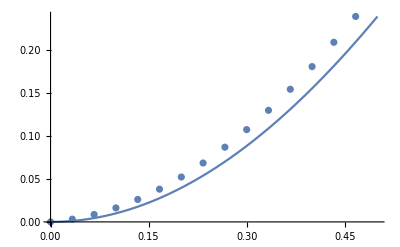

```mathematica
ψ[t_]:=-0.04374165462479168+0.4537437310186639*t

Res = SecantMethod[ψ];
Y = Y/.t->Res;

G1 = Plot[u[x], {x,a, b}];
G2 = ListPlot[Transpose[{X,Y}]];
Show[G1, G2]
(* Для получения большего приближения нужно увеличить n *)
```